```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
Subscript[ψ, F][x_,y_] = 1/Sqrt[2] * (Subscript[ϕ, 0][x]Subscript[ϕ, 1][y] - Subscript[ϕ, 0][y]Subscript[ϕ, 1][x] );
Subscript[ρ, F][x_,y_] = Integrate[Subscript[ψ, F][x,Subscript[x, 2]]*Subscript[ψ, F][y,Subscript[x, 2]], {Subscript[x, 2],-∞, ∞}];
Subscript[ρ, A][x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2]]*Subscript[ψ, F][y,Subscript[x, 2]], {Subscript[x, 2],x, y}];
Subscript[n, A][p_,κ_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, A][x,y,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->12,PrecisionGoal->12];
Subscript[n, F][p_] = 2/(2π) * Integrate[E^(I*p*(x-y))Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
```

```mathematica
Subscript[Φ, κ_]:= Subscript[Φ, κ]=Subscript[n, A][Range[-4,4,1/4],κ];
Subscript[data, κ_]:=Subscript[data, κ]=Thread[{Range[-4,4,1/4], Subscript[Φ, κ]}];
Subscript[f, κ_]:= Interpolation[Subscript[data, κ]];
```

```mathematica
Subscript[data, 0]={{-4,0.003152303821090666},{-15/4,0.004502641508881421},{-7/2,0.006741725273147649},{-13/4,0.010567912162491895},{-3,0.017079450978327165},{-11/4,0.02763931692903998},{-5/2,0.043212840687069966},{-9/4,0.0632072413499675},{-2,0.08502906116605075},{-7/4,0.10701776325284242},{-3/2,0.13633455660324323},{-5/4,0.19691493906127772},{-1,0.3245025238156466},{-3/4,0.5392545788469519},{-1/2,0.8095299898370808},{-1/4,1.044139768819599},{0,1.137958840069412},{1/4,1.044139768819599},{1/2,0.8095299898370808},{3/4,0.5392545788469519},{1,0.3245025238156466},{5/4,0.19691493906127772},{3/2,0.13633455660324323},{7/4,0.10701776325284242},{2,0.08502906116605075},{9/4,0.0632072413499675},{5/2,0.043212840687069966},{11/4,0.02763931692903998},{3,0.017079450978327165},{13/4,0.010567912162491895},{7/2,0.006741725273147649},{15/4,0.004502641508881421},{4,0.003152303821090666}};
Subscript[data, 1/3]={{-4,0.002348744397144807},{-15/4,0.003315711155114976},{-7/2,0.004836373722715486},{-13/4,0.007217383060374394},{-3,0.010787436206963236},{-11/4,0.01570606816027588},{-5/2,0.021824742258318652},{-9/4,0.029352164312883778},{-2,0.04162009894650295},{-7/4,0.070243026007817},{-3/2,0.1388351780057877},{-5/4,0.2764676283733927},{-1,0.49475289139945466},{-3/4,0.759270540585599},{-1/2,0.9848631854684363},{-1/4,1.076470597698474},{0,0.9945165262431741},{1/4,0.7878680300159591},{1/2,0.558975266986007},{3/4,0.39116845877398654},{1,0.3033315179498547},{5/4,0.2628171881484913},{3/2,0.22919580483352486},{7/4,0.1842890806240221},{2,0.13242421005165267},{9/4,0.08532327269446108},{5/2,0.05034622825217515},{11/4,0.028116337588111853},{3,0.015493192459786918},{13/4,0.008795937182585924},{7/2,0.00531063561658323},{15/4,0.0034446691202343113},{4,0.002380759022754451}};
Subscript[data, 2/3]={{-4,0.0007736400630160802},{-15/4,0.0010708083008496138},{-7/2,0.001499932403876583},{-13/4,0.0020948786950459775},{-3,0.0029091626470501143},{-11/4,0.004249839780600759},{-5/2,0.007570031124738098},{-9/4,0.017613118350425568},{-2,0.045606285342728606},{-7/4,0.11073960579797427},{-3/2,0.23419704730267085},{-5/4,0.421922566128276},{-1,0.643832252376574},{-3/4,0.8312003814727155},{-1/2,0.9096416574513474},{-1/4,0.8525296869763752},{0,0.7076318977795634},{1/4,0.5639271192938589},{1/2,0.48375373896891316},{3/4,0.4630982996736892},{1,0.45241087886926684},{5/4,0.4082721260576455},{3/2,0.32455767413040393},{7/4,0.22478566041418735},{2,0.13641039644788178},{9/4,0.0735842267319944},{5/2,0.03609151711859171},{11/4,0.016660109208450066},{3,0.007614918886657495},{13/4,0.003673432817238398},{7/2,0.0019741942977523153},{15/4,0.0011997662659924918},{4,0.0008056546886040054}};
```

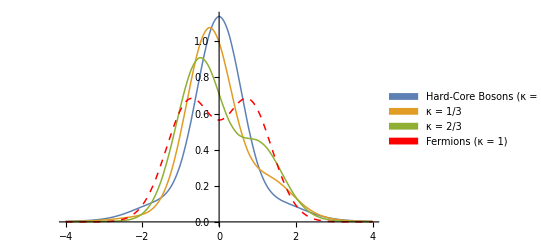

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/HCAMomentumDistributionPoster.png

```mathematica
Do[Subscript[f, i/3][p],{i,0,2}];
p1=Plot[{Subscript[f, 0][p],Subscript[f, 1/3][p],Subscript[f, 2/3][p],Subscript[n, F][p]},{p,-4,4},PlotLegends->SwatchLegend[{"Hard-Core Bosons (κ = 0)", "κ = 1/3","κ = 2/3", "Fermions (κ = 1)"}],PlotStyle->{Thickness[.0027],Thickness[.0027],Thickness[.0027],{Red,Dashed,Thickness[.0027]}},ImageSize->Scaled[0.6],BaseStyle->{FontWeight->Plain,FontFamily-> "Helvetica",FontSize-> 13}]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/HCAMomentumDistributionPoster.png",p1]
```

```mathematica
Take[$FontFamilies,200];
Style[#,FontFamily->#]&/@%
```

{Aharoni,Aldhabi,Alegreya SC,Andalus,Angsana New,AngsanaUPC,Aparajita,Arabic Transparent,Arabic Typesetting,Arial,Arial Baltic,Arial Black,Arial CE,Arial CYR,Arial Greek,Arial TUR,Batang,BatangChe,Bitstream Vera Sans Mono,Browallia New,BrowalliaUPC,Calibri,Calibri Light,Cambria,Cambria Math,Candara,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Comic Sans MS,Consolas,Constantia,Corbel,Cordia New,CordiaUPC,Courier,Courier New,Courier New Baltic,Courier New CE,Courier New CYR,Courier New Greek,Courier New TUR,Cousine,DaunPenh,David,DFKai-SB,DilleniaUPC,DokChampa,Dotum,DotumChe,Droid Serif,EB Garamond 08,EB Garamond 12,EB Garamond 12 All SC,EB Garamond SC 08,EB Garamond SC 12,Ebrima,Economica,Estrangelo Edessa,EucrosiaUPC,Euphemia,FangSong,Felipa,Fixedsys,Franklin Gothic Medium,FrankRuehl,FreesiaUPC,Gabriola,Gadugi,Gautami,Gentium Basic,Georgia,Gisha,Gulim,GulimChe,Gungsuh,GungsuhChe,Impact,Inconsolata,IrisUPC,Iskoola Pota,JasmineUPC,Javanese Text,KaiTi,Kalam,Kalam Bold,Kalam Light,Kalinga,Kartika,Khmer UI,KodchiangUPC,Kokila,Lao UI,Latha,Lato,Lato Black,Lato Hairline,Lato Light,League Gothic,League Gothic Condensed,League Gothic Condensed Italic,League Gothic Italic,Leelawadee,Leelawadee UI,Leelawadee UI Semilight,Levenim MT,LilyUPC,Lucida Console,Lucida Sans Unicode,Malgun Gothic,Mangal,Marlett,Meiryo,Meiryo UI,Microsoft Himalaya,Microsoft JhengHei,Microsoft JhengHei Light,Microsoft JhengHei UI,Microsoft JhengHei UI Light,Microsoft New Tai Lue,Microsoft PhagsPa,Microsoft Sans Serif,Microsoft Tai Le,Microsoft Uighur,Microsoft YaHei,Microsoft YaHei Light,Microsoft YaHei UI,Microsoft YaHei UI Light,Microsoft Yi Baiti,MingLiU,MingLiU-ExtB,MingLiU_HKSCS,MingLiU_HKSCS-ExtB,Miriam,Miriam Fixed,Modern,Mongolian Baiti,MoolBoran,MS Gothic,MS Mincho,MS PGothic,MS PMincho,MS Sans Serif,MS Serif,MS UI Gothic,MV Boli,Myanmar Text,Narkisim,Nirmala UI,Nirmala UI Semilight,NSimSun,Nyala,Oswald,Palatino Linotype,Plantagenet Cherokee,Playfair Display,Playfair Display Black,PMingLiU,PMingLiU-ExtB,Raavi,Roboto,Roboto Black,Roboto Condensed,Roboto Condensed Light,Roboto Light,Roboto Medium,Roboto Slab,Roboto Thin,Rod,Roman,Sakkal Majalla,Script,Segoe Print,Segoe Script,Segoe UI,Segoe UI Black,Segoe UI Emoji,Segoe UI Light,Segoe UI Semibold,Segoe UI Semilight,Segoe UI Symbol,Shadows Into Light Two,Shonar Bangla,Shruti,SimHei,Simplified Arabic,Simplified Arabic Fixed,SimSun,SimSun-ExtB,Sitka Banner,Sitka Display,Sitka Heading,Sitka Small,Sitka Subheading,Sitka Text,Small Fonts,Source Code Pro,Source Code Pro Black,Source Code Pro ExtraLight}